## Configuration

```mathematica
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];

(* 
This notebook tries to calculate the order(alpha_s tau) thrust rate in QCD. Question: do we need to include the virtual diagram to get the correct answer? My guess would be yes.
*)
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

Loading FeynCalc from /Users/Matt/Library/Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading FeynArts, see www.feynarts.de for documentation

FeynArts 3.7 patched for use with FeynCalc

Notebook load complete.

```mathematica
$LimitTo4//myPrint
turnOffConditional[];
```

$LimitTo4=False

```mathematica
$Assumptions=0<eps<1 && 0<M<Q&& 0<p1m<Q&&0<p1p<Q&&0<p2m<Q&&0<p2p<Q&&0<qm<Q&&0<qp<Q&&Q>0&&1/3>tau>0&&0<qhatp<1&&0<qhatm<1;

replSingVarPlus[e_]:=e/.PlusDistribution[a_*HeavisideTheta[b_]]:>HeavisideTheta[b-beta]a+DiracDelta[b-beta]Integrate[a,{tau,1,tau}];
expLogs[e_]:=e//.Log[a_/b_]:>Log[a]-Log[b]//.Log[a_*b_]:>Log[a]+Log[b]/.Log[a_^n_]:>  n*Log[a];

nondimensionalize[e_]:=e/.qm->qhatm*Q/.qp->qhatp*Q/.p1m->p1hatm*Q/.p1p->p1hatp*Q/.p2m->p2hatm*Q/.p2p->p2hatp*Q/.Vperp[p1]->Vperp[p1hat]*Q/.Vperp[p2]->Vperp[p2hat]*Q;
dimensionalize[e_]:=e/.qhatm->qm/Q/.qhatp->qp/Q/.p1hatm->p1m/Q/.p1hatp->p1p/Q/.p2hatm->p2m/Q/.p2hatp->p2p/Q;

(* 2 body kinematics for Vperp[k]=0 *)
kinematics2Body[e_]:=nondimensionalize[e]/.p1hatm->1/.p1hatp->0/.p2hatm->0/.p2hatp->1/.Vperp[p1hat]->0/.Vperp[p2hat]->0;

(* 3 body kinematics *)
varx=x23;
kinematics3Body[e_]:=nondimensionalize[e]/.Vperp[p1hat]->-Vperp[qhat]/.p2hatm->0/.p2hatp->1-qhatp-p1hatp/.p1hatp->qhatp*qhatm/p1hatm/.p1hatm->1-qhatm/.qhatp->x13*(1-qhatm)/.qhatm->x23/(1-x13);
If[varx==qhatm,
kinematics3Body[e_]:=nondimensionalize[e]/.Vperp[p1hat]->-Vperp[qhat]/.p2hatm->0/.p2hatp->1-qhatp-p1hatp/.p1hatp->qhatp*qhatm/p1hatm/.p1hatm->1-qhatm/.qhatp->x13*(1-qhatm)/.qhatm->x23/(1-x13)/.x23->qhatm*(1-x13);
];

(* the following from Collins A.43 and A.44 *)
phaseSpace2Dprefac=(Q^2/(16*Pi))^((D-4)/2)/(16*Sqrt[Pi]*Gamma[(D-1)/2])/.D->4-2*eps;
phaseSpace3Dprefac=(Q^2/(16*Pi))^((D-2)/2)*( Q^2/(4Pi))^(-eps)/(16*Sqrt[Pi]*Pi*Gamma[(D-1)/2]*Gamma[(D-2)/2])/.D->4-2*eps//Simplify
phaseSpace3Dprefac=(Q^2/(16*Pi^2))^((D-2)/2)*( Q^2/(4))^(-eps)/(16*Sqrt[Pi]*Gamma[(D-1)/2]*Gamma[(D-2)/2])/.D->4-2*eps//Simplify

Unprotect[Tr];
Tr/:Tr[0]:=0;
Protect[Tr];

c2=1+(alphabar/2)(-2/eps^2+(2Log[(-Q^2-I*delta)/muMS^2]-3)/eps-Log[(-Q^2-I*delta)/muMS^2]^2+3*Log[(-Q^2-I*delta)/muMS^2]+Pi^2/6-8);
(* below is the correction to the tree level amplitude squared due to virtual corrections *)
kFactor=((Series[c2*ComplexConjugate[c2],{alphabar,0,1}]//Normal//expLogs)/.Log[-Q^2+I*delta]->2Log[Q]+I*Pi/.Log[-Q^2-I*delta]->2Log[Q]-I*Pi//Simplify)/.Pi^2->zeta2*6//Expand;

spinSumHornig0g=-(MTD[mu,nu]-FVD[n+nb,mu]FVD[n+nb,nu]/4);
spinSumHornig=(-MTD[alpha,beta])(-(MTD[mu,nu]-FVD[n+nb,mu]FVD[n+nb,nu]/4));

spinSum0g=spinSumHornig0g;
spinSum=spinSumHornig;
```

(4^(3 ϵ-4) π^(2 ϵ-5/2) Q^(2-4 ϵ))/(1-ϵ 3/2-ϵ)

(4^(3 ϵ-4) π^(2 ϵ-5/2) Q^(2-4 ϵ))/(1-ϵ 3/2-ϵ)

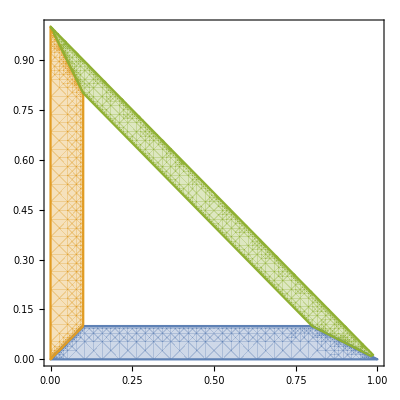

```mathematica
regA=x13<tau&&x13<x23&&x13<x12&&x13>0&&x23>0&&x12>0;
regB=x23<tau&&x23<x13&&x23<x12&&x13>0&&x23>0&&x12>0;
regC=x12<tau&&x12<x13&&x12<x23&&x13>0&&x23>0&&x12>0;
plotPS={regA,regB,regC}/.tau->0.1/.x12->1-x13-x23//kinematics3Body;
RegionPlot[plotPS,{x23,0,1},{x13,0,1},MaxRecursion->5]
```

## Integral Tables in Dalitz Space

```mathematica
(* we divide the integration into four disjoint regions  *)

(* Region A -- blue   -- the region where p2 has the largest energy  *)
(* Region B -- orange -- the region where p1 has the largest energy  *)
(* Region C -- green  -- the region where q has the largest energy   *)
(* Region τ -- white  -- the region where the thrust τ=1-T is larger than some value τ *)
(*
-Graphics-
(* ^Here the x-axis is x23 and the y-axis is x13 *)
*)

measure=(x13*x23*(1-x13-x23))^(eps);  (* The transformed measure from Collins FoPQCD eq. A44  *)
commonDenominator=x13*x23; 

(* the denominator that appears when we combine amplitudes squared *)
```

### Phase Space Integrals

#### A -- Sideways Integration (x-first)

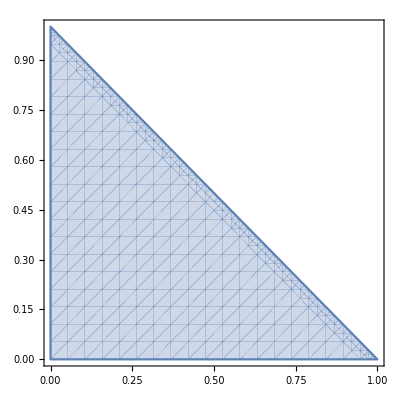

```mathematica
RegionPlot[z>x13/((1-x23)(x13+x23))/.z->1,{x13,0,1},{x23,0,1}]
```

```mathematica
(* try integrating x first, then y *)

(*
regAs1=Integrate[x^(n-1+eps)(1-x-y)^(eps),{x,y,1-2*y}];
regAs2=Integrate[%*y^(m-1+eps),{y,0,tau}];
regAs3=Series[%,{tau,0,2}]//Normal;
*)

(* it worked but the output is HUGE! Almost 57000 terms long *)

(* instead of keeping the huge result, we'll store the 4x4 {n,m} elements that are necessary for usual calculations *)
(* remember, the epsilons here are IR regulators, so negative. Later, use /.eps->negeps/.negeps->-eps to revert back to regular epsilons *)

regA00=-Pi^2/6+1/(2*ϵ^2)-2*τ-Log[τ]^2/2; 
regA01=τ*(1-Log[τ]);
regA02=0;
regA03=0;

regA10=-2+ϵ^(-1)-3*τ+Log[τ];
regA11=τ;
regA12=0;
regA13=0;

regA20=-1+1/(2*ϵ)-2*τ+Log[τ]/2;
regA21=τ/2;
regA22=0;
regA23=0;

regA30=-13/18+1/(3*ϵ)-2*τ+Log[τ]/3;
regA31=τ/3;
regA32=0;
regA33=0;
```

```mathematica
(*
Integrate[x^(0-1+eps)(1-x-y)^(eps),{x,y,1-2*y}]
Integrate[%*y^(0-1+eps),{y,0,tau}]
Series[%,{tau,0,4}]//Normal

Series[%,{tau,0,1}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%,{tau,0,1}]//Normal
*)
```

#### B -- Vertical Integration (y-first)

```mathematica
(* summary *)

regB00=regA00;
regB01=regA10;
regB02=regA20;
regB03=regA30;

regB10=regA01;
regB11=regA11;
regB12=regA21;
regB13=regA31;

regB20=regA02;
regB21=regA12;
regB22=regA22;
regB23=regA32;

regB30=regA03;
regB31=regA13;
regB32=regA23;
regB33=regA33;
```

```mathematica
(*
Integrate[y^(m-1+eps)(1-x-y)^(eps),{y,x,1-2*x}]
Integrate[%*x^(n-1+eps),{x,0,tau}]
regBlong=Series[%,{tau,0,2}]//Normal
*)

(* this is equivalent to the region A integration, but with n interchanged with m *)
```

#### C -- Sideways Integration (x-first)

```mathematica
(* summary *)

(* it looks like I only need to know the result for c02, c11, and c20, so let's just do those *)

(* remember, the epsilons here are IR regulators, so negative. Later, use /.eps->negeps/.negeps->-eps to revert back to regular epsilons *)

regC00=τ*(2-2*Log[τ]);
regC01=τ-τ*Log[τ];
regC02=-(τ*Log[τ]);
regC03=τ*(-1/2-Log[τ]);

regC10=τ*(1-Log[τ]);
regC11=τ;
regC12=τ/2;
regC13=τ/3;

regC20=-(τ*Log[τ]);
regC21=τ/2;
regC22=τ/6;
regC23=τ/12;

regC30=-(τ*(1+2*Log[τ]))/2;
regC31=τ/3;
regC32=τ/12;
regC33=τ/30;

intC[n_,m_]:=Switch[{n,m},{0,0},regC00 ,{0,1},regC01,{0,2},regC02,{0,3},regC03,{0,4},regC04,
							    {1,0},regC10 ,{1,1},regC11,{1,2},regC12,{1,3},regC13,{1,4},regC14,
						   	 {2,0},regC20 ,{2,1},regC21,{2,2},regC22,{2,3},regC23,{2,4},regC24,
						    	{3,0},regC30 ,{3,1},regC31,{3,2},regC32,{3,3},regC33,{3,4},regC34,
						    	{4,0},regC40 ,{4,1},regC41,{4,2},regC42,{4,3},regC43,{4,4},regC44]/.eps->-eps;
```

```mathematica
(* convert integrals from y to u=1-x-y *)
(* then the integration region has the same form as region A so we can try the sideways integration again *)

(*nn=1;
mm=1;

regCs02i=Integrate[x^(nn-1+eps)(1-x-u)^(mm-1+eps),{x,u,1-2*u}]

%/.Hypergeometric2F1Regularized[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1Regularized[a,b,c,d],eps,2]/.Hypergeometric2F1[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1[a,b,c,d],eps,2]/.Beta[z_,a_,b_]:>(z^a/a)*HypExp[Hypergeometric2F1[a,1-b,1+a,z],eps,2]

regCs02ii=Integrate[%*u^eps,{u,0,tau}]
regCs02=Series[%,{tau,0,2}];
regCs02=Series[%,{tau,0,1}]//Normal;
regCs02=Series[%,{eps,0,0}]//Normal
regCsnnmm=Series[%,{tau,0,1}]//Normal
regCsnnmm//InputForm*)
```

#### Overall

```mathematica
int00=regA00+regB00+regC00;
int01=regA01+regB01+regC01;
int02=regA02+regB02+regC02;
int03=regA03+regB03+regC03;

int10=regA10+regB10+regC10;
int11=regA11+regB11+regC11;
int12=regA12+regB12+regC12;
int13=regA13+regB13+regC13;

int20=regA20+regB20+regC20;
int21=regA21+regB21+regC21;
int22=regA22+regB22+regC22;
int23=regA23+regB23+regC23;

int30=regA30+regB30+regC30;
int31=regA31+regB31+regC31;
int32=regA32+regB32+regC32;
int33=regA33+regB33+regC33;

intTotal[n_,m_]:=Switch[{n,m},{0,0},int00 ,{0,1},int01,{0,2},int02,{0,3},int03,{0,4},int04,
							    {1,0},int10 ,{1,1},int11,{1,2},int12,{1,3},int13,{1,4},int14,
						   	 {2,0},int20 ,{2,1},int21,{2,2},int22,{2,3},int23,{2,4},int24,
						    	{3,0},int30 ,{3,1},int31,{3,2},int32,{3,3},int33,{3,4},int34,
						    	{4,0},int40 ,{4,1},int41,{4,2},int42,{4,3},int43,{4,4},int44]/.eps->-eps;
```

## Rate Calculation QCD for 0 gluons

### QCD 0g Vector

```mathematica
(* leading order vector amplitude *)
ampQCD0gV=I*SpinorUBar[p1].GAD[mu] .SpinorV[p2];
ampQCD0gVdag=-I*SpinorVBar[p2].GAD[nu] .SpinorU[p1];

ampQCD0gVtot=ampQCD0gV/.SpinorUBar[p1]->GSD[p1]/.a_ .SpinorV[p2]:>a;
ampQCD0gVdagtot=ampQCD0gVdag/.SpinorVBar[p2]:> GSD[p2]/.a_ .SpinorU[p1]:>a;
```

```mathematica
ampQCD0gVsqrtot=ampQCD0gVtot.ampQCD0gVdagtot*spinSum0g*V[f]

%//Contract//DiracSimplify//FCE//lcCompAll//gPerpDef
dTraceQCD0gV=Tr[%]//FCE//DiracSimplify//FCE   (* do the Dirac trace  *)

dTraceQCD0gV//dimensionalize
%//kinematics2Body//Simplify
%/.D->4-2*eps//Simplify

crossxQCD0gV=Nc*%*phaseSpace2Dprefac/(2*Q^2)/.V[f]->sumVf (* the 2Q^2 is from Hornig's cross section definition *)
(* don't expand ^, need the epsilon dependence to multiply into the 1/eps^2 and 1/eps virtual corrections *)
crossxQCDVborn=Series[%,{eps,0,0}]//Normal
```

V(f) (1/4 (n^μ+(n̄)^μ) (n^ν+(n̄)^ν)-g^μν) (ⅈ (γ·p_1).γ^μ).(-ⅈ (γ·p_2).γ^ν)

D V(f) (p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥)-2 V(f) (p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥)+1/4 V(f) (p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ·n).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥).(γ·n̄)+1/4 V(f) (p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ·n̄).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥).(γ·n)+1/2 p_2^+ V(f) (p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ·n)+1/2 p_2^- V(f) (p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ·n̄)

4 D V(f) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)+2 p_1^+ p_2^+ V(f)+2 p_1^- p_2^- V(f)-4 V(f) p_1_⊥·p_2_⊥-8 V(f) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)

4 D V(f) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)+2 p_1^+ p_2^+ V(f)+2 p_1^- p_2^- V(f)-4 V(f) p_1_⊥·p_2_⊥-8 V(f) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)

2 (D-2) Q^2 V(f)

-4 Q^2 (ϵ-1) V(f)

-(2^(4 ϵ-3) π^(ϵ-1/2) (ϵ-1) N_c (Q^2)^-ϵ Σ_(V(f)))/(1/2 (3-2 ϵ))

(N_c Σ_(V(f)))/(4 π)

### QCD 0g AxialVector

```mathematica
(* leading order vector amplitude *)
ampQCD0gA=I*SpinorUBar[p1].GAD[mu].GAD[5].SpinorV[p2];
ampQCD0gAdag=-I*SpinorVBar[p2].GAD[nu].GAD[5].SpinorU[p1];

ampQCD0gAtot=ampQCD0gA/.SpinorUBar[p1]->GSD[p1]/.a_ .SpinorV[p2]:>a;
ampQCD0gAdagtot=ampQCD0gAdag/.SpinorVBar[p2]:> GSD[p2]/.a_ .SpinorU[p1]:>a;
```

```mathematica
ampQCD0gAsqrtot=ampQCD0gAtot.ampQCD0gAdagtot*spinSum0g*A[f]

%//Contract//DiracSimplify//FCE//lcCompAll//gPerpDef
dTraceQCD0gA=Tr[%]//FCE//DiracSimplify//FCE   (* do the Dirac trace  *)

dTraceQCD0gA//dimensionalize
%//kinematics2Body//Simplify
%/.D->4-2*eps//Simplify

crossxQCD0gA=Nc*%*phaseSpace2Dprefac/(2*Q^2)/.A[f]->sumAf (* the 2Q^2 is from Hornig's cross section definition *)
crossxQCDAborn=Series[%,{eps,0,0}]//Normal
```

A(f) (1/4 (n^μ+(n̄)^μ) (n^ν+(n̄)^ν)-g^μν) (ⅈ (γ·p_1).γ^μ.γ^5).(-ⅈ (γ·p_2).γ^ν.γ^5)

D A(f) (p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥)-2 A(f) (p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥)+1/4 A(f) (p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ·n).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥).(γ·n̄)+1/4 A(f) (p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ·n̄).(p_2^- γ·n/2+p_2^+ γ·(n̄)/2+γ·p_2_⊥).(γ·n)+1/2 p_2^+ A(f) (p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ·n)+1/2 p_2^- A(f) (p_1^- γ·n/2+p_1^+ γ·(n̄)/2+γ·p_1_⊥).(γ·n̄)

4 D A(f) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)+2 p_1^+ p_2^+ A(f)+2 p_1^- p_2^- A(f)-4 A(f) p_1_⊥·p_2_⊥-8 A(f) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)

4 D A(f) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)+2 p_1^+ p_2^+ A(f)+2 p_1^- p_2^- A(f)-4 A(f) p_1_⊥·p_2_⊥-8 A(f) (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)

2 (D-2) Q^2 A(f)

-4 Q^2 (ϵ-1) A(f)

-(2^(4 ϵ-3) π^(ϵ-1/2) (ϵ-1) Σ_(A(f)) N_c (Q^2)^-ϵ)/(1/2 (3-2 ϵ))

(Σ_(A(f)) N_c)/(4 π)

## Rate Calculation QCD for 1 gluon

### QCD 1g Vector

```mathematica
(* leading order vector amplitude *)
ampQCDV=-I*g*Ta*SpinorUBar[p1].(  ((2*FVD[p1,alpha]+GAD[alpha].GSD[q])/(2*SPD[p1,q])).GAD[mu] - GAD[mu].((2*FVD[p2,alpha]+GSD[q].GAD[alpha])/(2*SPD[p2,q]))  ).SpinorV[p2]//DeltaDef;
ampQCDVdag=I*g*Tb*SpinorVBar[p2].(  GAD[nu].((2*FVD[p1,beta]+GSD[q].GAD[beta])/(2*SPD[p1,q]))- ((2*FVD[p2,beta]+GAD[beta].GSD[q])/(2*SPD[p2,q])).GAD[nu]  ).SpinorU[p1]//DeltaDef;

ampQCDVtot=ampQCDV/.SpinorUBar[p1]->GSD[p1]/.a_ .SpinorV[p2]:>a;
ampQCDVdagtot=ampQCDVdag/.SpinorVBar[p2]:> GSD[p2]/.a_ .SpinorU[p1]:>a;
```

```mathematica
ampQCDVsqrtot=ampQCDVdagtot.ampQCDVtot*spinSum*V[f]
%//Contract//DiracSimplify//FCE;
ampQCDVsqrtot=%/.SpinorU[p1].SpinorUBar[p1]->GSD[p1]/.SpinorVBar[p2]->GSD[p2]/.a_ .SpinorV[p2].b_:>a.b/.a_ .SpinorV[p2]:>a//DeltaDef//DiracSimplify//FCE;
evalthisQCDV=ampQCDVsqrtot;

evalthisQCDV/.Ta*Tb->Cf//PhatDef//lcCompAll
%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE;
%//gPerpDef;
dTraceQCDV=Tr[%]//FCE//DiracSimplify//FCE;   (* do the Dirac trace  *)

dTraceQCDV//kinematics3Body;
%//Simplify
%/.D->4-2*eps//Simplify;
QCDV=Series[%,{eps,0,1}]//Normal
```

V(f) g^αβ (1/4 (n^μ+(n̄)^μ) (n^ν+(n̄)^ν)-g^μν) (-(ⅈ g T^b (γ·p_2).(γ^ν.(2 p_1^β+(γ·q).γ^β)/(2 p_1·q)-(2 p_2^β+γ^β.(γ·q))/(2 p_2·q).γ^ν)).(-ⅈ g T^a (γ·p_1).((2 p_1^α+γ^α.(γ·q))/(2 p_1·q).γ^μ-γ^μ.(2 p_2^α+(γ·q).γ^α)/(2 p_2·q))))

-(2 C_F (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-) V(f) g^2)/(1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥)+(C_F D (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-) V(f) g^2)/(1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥)+(C_F D^2 (γ·p_2_⊥+γ·1 1+γ·n/2 p_2^-).1 V(f) g^2)/(2 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+173+(C_F (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n̄).(γ·n).(γ·q_⊥+γ·27/2 q^++γ·n/2 q^-) (1/2 q^+ p_1^-+1+1) V(f) g^2)/(4 (1/2 q^+ p_2^-+1/2 p_2^+ q^-+p_2_⊥·q_⊥)^2)-(C_F D (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n̄).(γ·n).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-) (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥) V(f) g^2)/(8 (1/2 q^+ p_2^-+1/2 p_2^+ q^-+p_2_⊥·q_⊥)^2)
 |  |  |  |

(2 g^2 C_F V(f) (D^2 (x13+x23)^2-4 D (x13^2+3 x13 x23+x13+x23^2+x23-1)+4 (x13^2+x13 (4 x23+2)+x23^2+2 x23-2)))/(x13 x23)

(8 g^2 C_F V(f) (x13^2-2 x13+x23^2-2 x23+2))/(x13 x23)-(16 g^2 ϵ C_F V(f) (x13^2+x13 x23-x13+x23^2-x23+1))/(x13 x23)

```mathematica
igrandV[n_,m_]:=SeriesCoefficient[QCDV*commonDenominator,{varx,0,n},{x13,0,m}];

check=QCDV-Sum[varx^i*x13^j*igrandV[i,j]/commonDenominator,{i,0,4},{j,0,4}]//Simplify

Nc*phaseSpace3Dprefac*Sum[igrandV[i,j]intTotal[i,j],{i,0,3},{j,0,3}]/.V[f]->sumVf
%/.g^2->(8Pi^2*alphabar/Cf)*(muMS^2*Exp[EulerGamma]/(4*Pi))^eps//Simplify
Series[%,{eps,0,0}]//Normal
%/.PolyGamma[0,3/2]->2-EulerGamma-Log[4]//expLogs//Expand
%//Simplify
crossxQCDV=%/(2*Q^2)//Simplify (* the 2Q^2 is from Hornig's cross section definition *)
```

0

1/(1-ϵ 3/2-ϵ)4^(3 ϵ-4) π^(2 ϵ-5/2) N_c Q^(2-4 ϵ) ((-4 τ-log^2(τ)+τ (2-2 log(τ))+1/ϵ^2-π^2/3) (16 g^2 C_F Σ_(V(f))-16 g^2 ϵ C_F Σ_(V(f)))-48 g^2 τ ϵ C_F Σ_(V(f))+(-3 τ+2 τ (1-log(τ))+log(τ)-1/ϵ-2) (16 g^2 ϵ C_F Σ_(V(f))-16 g^2 C_F Σ_(V(f)))+2 (-2 τ+τ (-log(τ))+(log(τ))/2-1/(2 ϵ)-1) (8 g^2 C_F Σ_(V(f))-16 g^2 ϵ C_F Σ_(V(f)))+(-2 τ+τ (1-log(τ))-τ log(τ)+log(τ)-1/ϵ-2) (16 g^2 ϵ C_F Σ_(V(f))-16 g^2 C_F Σ_(V(f))))

(4^(2 ϵ-1) ⅇ^(ℽ ϵ) π^(ϵ-1/2) ᾱ N_c Q^(2-4 ϵ) Σ_(V(f)) (μ_OverBar[MS]^2)^ϵ (2 (3 τ+π^2-6) ϵ^3-2 (6 τ+π^2-6) ϵ^2+6 (ϵ-1) ϵ^2 log^2(τ)+3 ϵ^2 log(τ) (2 τ+2 ϵ-3)+3 ϵ+6))/(3 ϵ^2 1-ϵ 3/2-ϵ)

-1/(6 π)Q^2 ᾱ N_c Σ_(V(f)) (24 log(Q) log(μ_OverBar[MS]^2)-3 log^2(μ_OverBar[MS]^2)-6 log(π) log(μ_OverBar[MS]^2)-12 log(4) log(μ_OverBar[MS]^2)-3 log(μ_OverBar[MS]^2)-6 03/2 log(μ_OverBar[MS]^2)-48 log^2(Q)+24 log(π) log(Q)+48 log(4) log(Q)+12 log(Q)+24 03/2 log(Q)+12 τ+6 log^2(τ)-6 τ log(τ)+9 log(τ)+4 π^2-24-3 log^2(π)-12 log^2(4)-12 log(4) log(π)-3 log(π)-6 log(4)-3 (03/2)^2-3 03/2-6 log(π) 03/2-12 log(4) 03/2)+(Q^2 ᾱ N_c Σ_(V(f)) (2 log(μ_OverBar[MS]^2)-8 log(Q)+1+2 log(π)+4 log(4)+2 03/2))/(2 π ϵ)+(Q^2 ᾱ N_c Σ_(V(f)))/(π ϵ^2)

(2 Q^2 ᾱ N_c Σ_(V(f)) log^2(μ_OverBar[MS]))/π-(2 ℽ Q^2 ᾱ N_c Σ_(V(f)) log(μ_OverBar[MS]))/π+(5 Q^2 ᾱ N_c Σ_(V(f)) log(μ_OverBar[MS]))/π+(2 Q^2 log(4) ᾱ N_c Σ_(V(f)) log(μ_OverBar[MS]))/π-(8 Q^2 ᾱ N_c log(Q) Σ_(V(f)) log(μ_OverBar[MS]))/π+(2 Q^2 log(π) ᾱ N_c Σ_(V(f)) log(μ_OverBar[MS]))/π+(2 Q^2 ᾱ N_c Σ_(V(f)) log(μ_OverBar[MS]))/(π ϵ)-(2 Q^2 τ ᾱ N_c Σ_(V(f)))/π-(Q^2 ᾱ N_c log^2(τ) Σ_(V(f)))/π-(3 Q^2 ᾱ N_c log(τ) Σ_(V(f)))/(2 π)+(Q^2 τ ᾱ N_c log(τ) Σ_(V(f)))/π-2/3 π Q^2 ᾱ N_c Σ_(V(f))+(ℽ^2 Q^2 ᾱ N_c Σ_(V(f)))/(2 π)-(5 ℽ Q^2 ᾱ N_c Σ_(V(f)))/(2 π)+(7 Q^2 ᾱ N_c Σ_(V(f)))/π+(8 Q^2 ᾱ N_c log^2(Q) Σ_(V(f)))/π+(Q^2 log^2(π) ᾱ N_c Σ_(V(f)))/(2 π)+(Q^2 log^2(4) ᾱ N_c Σ_(V(f)))/(2 π)+(4 ℽ Q^2 ᾱ N_c log(Q) Σ_(V(f)))/π-(10 Q^2 ᾱ N_c log(Q) Σ_(V(f)))/π-(4 Q^2 log(π) ᾱ N_c log(Q) Σ_(V(f)))/π-(4 Q^2 log(4) ᾱ N_c log(Q) Σ_(V(f)))/π-(ℽ Q^2 log(π) ᾱ N_c Σ_(V(f)))/π+(5 Q^2 log(π) ᾱ N_c Σ_(V(f)))/(2 π)+(Q^2 log(4) log(π) ᾱ N_c Σ_(V(f)))/π-(ℽ Q^2 log(4) ᾱ N_c Σ_(V(f)))/π+(5 Q^2 log(4) ᾱ N_c Σ_(V(f)))/(2 π)+(Q^2 ᾱ N_c Σ_(V(f)))/(π ϵ^2)-(ℽ Q^2 ᾱ N_c Σ_(V(f)))/(π ϵ)+(5 Q^2 ᾱ N_c Σ_(V(f)))/(2 π ϵ)-(4 Q^2 ᾱ N_c log(Q) Σ_(V(f)))/(π ϵ)+(Q^2 log(π) ᾱ N_c Σ_(V(f)))/(π ϵ)+(Q^2 log(4) ᾱ N_c Σ_(V(f)))/(π ϵ)

1/(6 π ϵ^2)Q^2 ᾱ N_c Σ_(V(f)) (-6 ϵ log(μ_OverBar[MS]) (8 ϵ log(Q)+ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)+12 ϵ^2 log^2(μ_OverBar[MS])+48 ϵ^2 log^2(Q)+12 ϵ log(Q) (ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)-12 τ ϵ^2-6 ϵ^2 log^2(τ)+6 τ ϵ^2 log(τ)-9 ϵ^2 log(τ)-4 π^2 ϵ^2+3 ℽ^2 ϵ^2-15 ℽ ϵ^2+42 ϵ^2+3 ϵ^2 log^2(π)+3 ϵ^2 log^2(4)+6 ϵ^2 log(4) log(π)-6 ℽ ϵ^2 log(π)+15 ϵ^2 log(π)-6 ℽ ϵ^2 log(4)+15 ϵ^2 log(4)-6 ℽ ϵ+15 ϵ+6 ϵ log(π)+6 ϵ log(4)+6)

1/(12 π ϵ^2)ᾱ N_c Σ_(V(f)) (-6 ϵ log(μ_OverBar[MS]) (8 ϵ log(Q)+ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)+12 ϵ^2 log^2(μ_OverBar[MS])+48 ϵ^2 log^2(Q)+12 ϵ log(Q) (ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)-12 τ ϵ^2-6 ϵ^2 log^2(τ)+6 τ ϵ^2 log(τ)-9 ϵ^2 log(τ)-4 π^2 ϵ^2+3 ℽ^2 ϵ^2-15 ℽ ϵ^2+42 ϵ^2+3 ϵ^2 log^2(π)+3 ϵ^2 log^2(4)+6 ϵ^2 log(4) log(π)-6 ℽ ϵ^2 log(π)+15 ϵ^2 log(π)-6 ℽ ϵ^2 log(4)+15 ϵ^2 log(4)-6 ℽ ϵ+15 ϵ+6 ϵ log(π)+6 ϵ log(4)+6)

### QCD 1g AxialVector

```mathematica
(* leading order vector amplitude *)
ampQCDA=-I*g*Ta*SpinorUBar[p1].(  ((2*FVD[p1,alpha]+GAD[alpha].GSD[q])/(2*SPD[p1,q])).GAD[mu].GAD[5] - GAD[mu].GAD[5].((2*FVD[p2,alpha]+GSD[q].GAD[alpha])/(2*SPD[p2,q]))  ).SpinorV[p2]//DeltaDef;
ampQCDAdag=I*g*Tb*SpinorVBar[p2].(  GAD[nu].GAD[5] .((2*FVD[p1,beta]+GSD[q].GAD[beta])/(2*SPD[p1,q]))- ((2*FVD[p2,beta]+GAD[beta].GSD[q])/(2*SPD[p2,q])).GAD[nu].GAD[5]   ).SpinorU[p1]//DeltaDef;

ampQCDAtot=ampQCDA/.SpinorUBar[p1]->GSD[p1]/.a_ .SpinorV[p2]:>a;
ampQCDAdagtot=ampQCDAdag/.SpinorVBar[p2]:> GSD[p2]/.a_ .SpinorU[p1]:>a;
```

```mathematica
ampQCDAsqrtot=ampQCDAdagtot.ampQCDAtot*spinSum*A[f]
%//Contract//DiracSimplify//FCE;
ampQCDAsqrtot=%/.SpinorU[p1].SpinorUBar[p1]->GSD[p1]/.SpinorVBar[p2]->GSD[p2]/.a_ .SpinorV[p2].b_:>a.b/.a_ .SpinorV[p2]:>a//DeltaDef//DiracSimplify//FCE;
evalthisQCDA=ampQCDAsqrtot;

evalthisQCDA/.Ta*Tb->Cf//PhatDef//lcCompAll
%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE;
%//gPerpDef;
dTraceQCDA=Tr[%]//FCE//DiracSimplify//FCE;   (* do the Dirac trace  *)

dTraceQCDA//kinematics3Body;
%//Simplify
%/.D->4-2*eps//Simplify;
QCDA=Series[%,{eps,0,1}]//Normal
```

-A(f) g^αβ (1/4 (n^μ+(n̄)^μ) (n^ν+(n̄)^ν)-g^μν) (ⅈ g T^b (γ·p_2).(γ^ν.γ^5.(2 p_1^β+(γ·q).γ^β)/(2 p_1·q)-(2 p_2^β+γ^β.(γ·q))/(2 p_2·q).γ^ν.γ^5)).(-ⅈ g T^a (γ·p_1).((2 p_1^α+γ^α.(γ·q))/(2 p_1·q).γ^μ.γ^5-γ^μ.γ^5.(2 p_2^α+(γ·q).γ^α)/(2 p_2·q)))

-(2 C_F A(f) (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-) g^2)/(1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥)+(C_F D A(f) (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-) g^2)/(1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥)+(C_F D^2 A(f) (γ·p_2_⊥+γ·27/2 p_2^++γ·n/2 p_2^-).(1) g^2)/(2 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+177+1-(C_F D 3 g^2)/(8 1^2)+(C_F A(f) (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·27).(γ·n).(γ·q_⊥+γ·27/2 q^++γ·n/2 q^-) (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥) g^2)/(4 (1/2 q^+ p_2^-+1/2 p_2^+ q^-+p_2_⊥·q_⊥)^2)-(C_F D A(f) (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n̄).(γ·n).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-) (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥) g^2)/(8 (1/2 q^+ p_2^-+1/2 p_2^+ q^-+p_2_⊥·q_⊥)^2)
 |  |  |  |

(2 g^2 A(f) C_F (D^2 (x13+x23)^2-4 D (x13^2+3 x13 x23+x13+x23^2+x23-1)+4 (x13^2+x13 (4 x23+2)+x23^2+2 x23-2)))/(x13 x23)

(8 g^2 A(f) C_F (x13^2-2 x13+x23^2-2 x23+2))/(x13 x23)-(16 g^2 ϵ A(f) C_F (x13^2+x13 x23-x13+x23^2-x23+1))/(x13 x23)

```mathematica
igrandA[n_,m_]:=SeriesCoefficient[QCDA*commonDenominator,{varx,0,n},{x13,0,m}];

check=QCDA-Sum[varx^i*x13^j*igrandA[i,j]/commonDenominator,{i,0,4},{j,0,4}]//Simplify

Nc*phaseSpace3Dprefac*Sum[igrandA[i,j]intTotal[i,j],{i,0,3},{j,0,3}]/.A[f]->sumAf
%/.g^2->(8Pi^2*alphabar/Cf)*(muMS^2*Exp[EulerGamma]/(4*Pi))^eps//Simplify
Series[%,{eps,0,0}]//Normal
%/.PolyGamma[0,3/2]->2-EulerGamma-Log[4]//expLogs//Expand
%(*/.Log[Q]->LQ/2+Log[muMS]*)//Simplify
crossxQCDA=%/(2*Q^2)//Simplify(* the 2Q^2 is from Hornig's cross section definition *)
```

0

1/(1-ϵ 3/2-ϵ)4^(3 ϵ-4) π^(2 ϵ-5/2) N_c Q^(2-4 ϵ) ((-4 τ-log^2(τ)+τ (2-2 log(τ))+1/ϵ^2-π^2/3) (16 g^2 Σ_(A(f)) C_F-16 g^2 ϵ Σ_(A(f)) C_F)-48 g^2 τ ϵ Σ_(A(f)) C_F+(-3 τ+2 τ (1-log(τ))+log(τ)-1/ϵ-2) (16 g^2 ϵ Σ_(A(f)) C_F-16 g^2 Σ_(A(f)) C_F)+2 (-2 τ+τ (-log(τ))+(log(τ))/2-1/(2 ϵ)-1) (8 g^2 Σ_(A(f)) C_F-16 g^2 ϵ Σ_(A(f)) C_F)+(-2 τ+τ (1-log(τ))-τ log(τ)+log(τ)-1/ϵ-2) (16 g^2 ϵ Σ_(A(f)) C_F-16 g^2 Σ_(A(f)) C_F))

(4^(2 ϵ-1) ⅇ^(ℽ ϵ) π^(ϵ-1/2) ᾱ Σ_(A(f)) N_c Q^(2-4 ϵ) (μ_OverBar[MS]^2)^ϵ (2 (3 τ+π^2-6) ϵ^3-2 (6 τ+π^2-6) ϵ^2+6 (ϵ-1) ϵ^2 log^2(τ)+3 ϵ^2 log(τ) (2 τ+2 ϵ-3)+3 ϵ+6))/(3 ϵ^2 1-ϵ 3/2-ϵ)

-1/(6 π)Q^2 ᾱ Σ_(A(f)) N_c (24 log(Q) log(μ_OverBar[MS]^2)-3 log^2(μ_OverBar[MS]^2)-6 log(π) log(μ_OverBar[MS]^2)-12 log(4) log(μ_OverBar[MS]^2)-3 log(μ_OverBar[MS]^2)-6 03/2 log(μ_OverBar[MS]^2)-48 log^2(Q)+24 log(π) log(Q)+48 log(4) log(Q)+12 log(Q)+24 03/2 log(Q)+12 τ+6 log^2(τ)-6 τ log(τ)+9 log(τ)+4 π^2-24-3 log^2(π)-12 log^2(4)-12 log(4) log(π)-3 log(π)-6 log(4)-3 (03/2)^2-3 03/2-6 log(π) 03/2-12 log(4) 03/2)+(Q^2 ᾱ Σ_(A(f)) N_c (2 log(μ_OverBar[MS]^2)-8 log(Q)+1+2 log(π)+4 log(4)+2 03/2))/(2 π ϵ)+(Q^2 ᾱ Σ_(A(f)) N_c)/(π ϵ^2)

(2 Q^2 ᾱ Σ_(A(f)) N_c log^2(μ_OverBar[MS]))/π-(2 ℽ Q^2 ᾱ Σ_(A(f)) N_c log(μ_OverBar[MS]))/π+(5 Q^2 ᾱ Σ_(A(f)) N_c log(μ_OverBar[MS]))/π+(2 Q^2 log(4) ᾱ Σ_(A(f)) N_c log(μ_OverBar[MS]))/π-(8 Q^2 ᾱ Σ_(A(f)) N_c log(Q) log(μ_OverBar[MS]))/π+(2 Q^2 log(π) ᾱ Σ_(A(f)) N_c log(μ_OverBar[MS]))/π+(2 Q^2 ᾱ Σ_(A(f)) N_c log(μ_OverBar[MS]))/(π ϵ)-(2 Q^2 τ ᾱ Σ_(A(f)) N_c)/π-(Q^2 ᾱ Σ_(A(f)) N_c log^2(τ))/π-(3 Q^2 ᾱ Σ_(A(f)) N_c log(τ))/(2 π)+(Q^2 τ ᾱ Σ_(A(f)) N_c log(τ))/π-2/3 π Q^2 ᾱ Σ_(A(f)) N_c+(ℽ^2 Q^2 ᾱ Σ_(A(f)) N_c)/(2 π)-(5 ℽ Q^2 ᾱ Σ_(A(f)) N_c)/(2 π)+(7 Q^2 ᾱ Σ_(A(f)) N_c)/π+(8 Q^2 ᾱ Σ_(A(f)) N_c log^2(Q))/π+(Q^2 log^2(π) ᾱ Σ_(A(f)) N_c)/(2 π)+(Q^2 log^2(4) ᾱ Σ_(A(f)) N_c)/(2 π)+(4 ℽ Q^2 ᾱ Σ_(A(f)) N_c log(Q))/π-(10 Q^2 ᾱ Σ_(A(f)) N_c log(Q))/π-(4 Q^2 log(π) ᾱ Σ_(A(f)) N_c log(Q))/π-(4 Q^2 log(4) ᾱ Σ_(A(f)) N_c log(Q))/π-(ℽ Q^2 log(π) ᾱ Σ_(A(f)) N_c)/π+(5 Q^2 log(π) ᾱ Σ_(A(f)) N_c)/(2 π)+(Q^2 log(4) log(π) ᾱ Σ_(A(f)) N_c)/π-(ℽ Q^2 log(4) ᾱ Σ_(A(f)) N_c)/π+(5 Q^2 log(4) ᾱ Σ_(A(f)) N_c)/(2 π)+(Q^2 ᾱ Σ_(A(f)) N_c)/(π ϵ^2)-(ℽ Q^2 ᾱ Σ_(A(f)) N_c)/(π ϵ)+(5 Q^2 ᾱ Σ_(A(f)) N_c)/(2 π ϵ)-(4 Q^2 ᾱ Σ_(A(f)) N_c log(Q))/(π ϵ)+(Q^2 log(π) ᾱ Σ_(A(f)) N_c)/(π ϵ)+(Q^2 log(4) ᾱ Σ_(A(f)) N_c)/(π ϵ)

1/(6 π ϵ^2)Q^2 ᾱ Σ_(A(f)) N_c (-6 ϵ log(μ_OverBar[MS]) (8 ϵ log(Q)+ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)+12 ϵ^2 log^2(μ_OverBar[MS])+48 ϵ^2 log^2(Q)+12 ϵ log(Q) (ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)-12 τ ϵ^2-6 ϵ^2 log^2(τ)+6 τ ϵ^2 log(τ)-9 ϵ^2 log(τ)-4 π^2 ϵ^2+3 ℽ^2 ϵ^2-15 ℽ ϵ^2+42 ϵ^2+3 ϵ^2 log^2(π)+3 ϵ^2 log^2(4)+6 ϵ^2 log(4) log(π)-6 ℽ ϵ^2 log(π)+15 ϵ^2 log(π)-6 ℽ ϵ^2 log(4)+15 ϵ^2 log(4)-6 ℽ ϵ+15 ϵ+6 ϵ log(π)+6 ϵ log(4)+6)

1/(12 π ϵ^2)ᾱ Σ_(A(f)) N_c (-6 ϵ log(μ_OverBar[MS]) (8 ϵ log(Q)+ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)+12 ϵ^2 log^2(μ_OverBar[MS])+48 ϵ^2 log^2(Q)+12 ϵ log(Q) (ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)-12 τ ϵ^2-6 ϵ^2 log^2(τ)+6 τ ϵ^2 log(τ)-9 ϵ^2 log(τ)-4 π^2 ϵ^2+3 ℽ^2 ϵ^2-15 ℽ ϵ^2+42 ϵ^2+3 ϵ^2 log^2(π)+3 ϵ^2 log^2(4)+6 ϵ^2 log(4) log(π)-6 ℽ ϵ^2 log(π)+15 ϵ^2 log(π)-6 ℽ ϵ^2 log(4)+15 ϵ^2 log(4)-6 ℽ ϵ+15 ϵ+6 ϵ log(π)+6 ϵ log(4)+6)

## Total Rate

```mathematica
(crossxQCDVborn+crossxQCDAborn)//FullSimplify
```

(N_c (Σ_(A(f))+Σ_(V(f))))/(4 π)

```mathematica
(crossxQCD0gV+crossxQCD0gA)*kFactor+(crossxQCDV+crossxQCDA)
%/(crossxQCDVborn+crossxQCDAborn)
Series[%,{eps,0,0}]//Normal
Series[%,{tau,0,1}]//Normal
%/.PolyGamma[0,3/2]->2-EulerGamma-Log[4]//expLogs//Expand
%/.Pi^2->6zeta2(*/.Log[Q]->LQ/2+Log[muMS]*)//Expand
rate=%//FullSimplify
```

(7 ζ_2 ᾱ-(2 ᾱ)/ϵ^2-(3 ᾱ)/ϵ-8 ᾱ+8 ᾱ log(Q) log(μ_OverBar[MS])-(4 ᾱ log(μ_OverBar[MS]))/ϵ-4 ᾱ log^2(μ_OverBar[MS])-6 ᾱ log(μ_OverBar[MS])+(4 ᾱ log(Q))/ϵ-4 ᾱ log^2(Q)+6 ᾱ log(Q)+1) (-(2^(4 ϵ-3) π^(ϵ-1/2) (ϵ-1) Σ_(A(f)) N_c (Q^2)^-ϵ)/(1/2 (3-2 ϵ))-(2^(4 ϵ-3) π^(ϵ-1/2) (ϵ-1) N_c (Q^2)^-ϵ Σ_(V(f)))/(1/2 (3-2 ϵ)))+1/(12 π ϵ^2)ᾱ Σ_(A(f)) N_c (-6 ϵ log(μ_OverBar[MS]) (8 ϵ log(Q)+ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)+12 ϵ^2 log^2(μ_OverBar[MS])+48 ϵ^2 log^2(Q)+12 ϵ log(Q) (ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)-12 τ ϵ^2-6 ϵ^2 log^2(τ)+6 τ ϵ^2 log(τ)-9 ϵ^2 log(τ)-4 π^2 ϵ^2+3 ℽ^2 ϵ^2-15 ℽ ϵ^2+42 ϵ^2+3 ϵ^2 log^2(π)+3 ϵ^2 log^2(4)+6 ϵ^2 log(4) log(π)-6 ℽ ϵ^2 log(π)+15 ϵ^2 log(π)-6 ℽ ϵ^2 log(4)+15 ϵ^2 log(4)-6 ℽ ϵ+15 ϵ+6 ϵ log(π)+6 ϵ log(4)+6)+1/(12 π ϵ^2)ᾱ N_c Σ_(V(f)) (-6 ϵ log(μ_OverBar[MS]) (8 ϵ log(Q)+ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)+12 ϵ^2 log^2(μ_OverBar[MS])+48 ϵ^2 log^2(Q)+12 ϵ log(Q) (ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)-12 τ ϵ^2-6 ϵ^2 log^2(τ)+6 τ ϵ^2 log(τ)-9 ϵ^2 log(τ)-4 π^2 ϵ^2+3 ℽ^2 ϵ^2-15 ℽ ϵ^2+42 ϵ^2+3 ϵ^2 log^2(π)+3 ϵ^2 log^2(4)+6 ϵ^2 log(4) log(π)-6 ℽ ϵ^2 log(π)+15 ϵ^2 log(π)-6 ℽ ϵ^2 log(4)+15 ϵ^2 log(4)-6 ℽ ϵ+15 ϵ+6 ϵ log(π)+6 ϵ log(4)+6)

1/((Σ_(A(f)) N_c)/(4 π)+(N_c Σ_(V(f)))/(4 π))((7 ζ_2 ᾱ-(2 ᾱ)/ϵ^2-(3 ᾱ)/ϵ-8 ᾱ+8 ᾱ log(Q) log(μ_OverBar[MS])-(4 ᾱ log(μ_OverBar[MS]))/ϵ-4 ᾱ log^2(μ_OverBar[MS])-6 ᾱ log(μ_OverBar[MS])+(4 ᾱ log(Q))/ϵ-4 ᾱ log^2(Q)+6 ᾱ log(Q)+1) (-(2^(4 ϵ-3) π^(ϵ-1/2) (ϵ-1) Σ_(A(f)) N_c (Q^2)^-ϵ)/(1/2 (3-2 ϵ))-(2^(4 ϵ-3) π^(ϵ-1/2) (ϵ-1) N_c (Q^2)^-ϵ Σ_(V(f)))/(1/2 (3-2 ϵ)))+1/(12 π ϵ^2)ᾱ Σ_(A(f)) N_c (-6 ϵ log(μ_OverBar[MS]) (8 ϵ log(Q)+ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)+12 ϵ^2 log^2(μ_OverBar[MS])+48 ϵ^2 log^2(Q)+12 ϵ log(Q) (ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)-12 τ ϵ^2-6 ϵ^2 log^2(τ)+6 τ ϵ^2 log(τ)-9 ϵ^2 log(τ)-4 π^2 ϵ^2+3 ℽ^2 ϵ^2-15 ℽ ϵ^2+42 ϵ^2+3 ϵ^2 log^2(π)+3 ϵ^2 log^2(4)+6 ϵ^2 log(4) log(π)-6 ℽ ϵ^2 log(π)+15 ϵ^2 log(π)-6 ℽ ϵ^2 log(4)+15 ϵ^2 log(4)-6 ℽ ϵ+15 ϵ+6 ϵ log(π)+6 ϵ log(4)+6)+1/(12 π ϵ^2)ᾱ N_c Σ_(V(f)) (-6 ϵ log(μ_OverBar[MS]) (8 ϵ log(Q)+ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)+12 ϵ^2 log^2(μ_OverBar[MS])+48 ϵ^2 log^2(Q)+12 ϵ log(Q) (ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)-12 τ ϵ^2-6 ϵ^2 log^2(τ)+6 τ ϵ^2 log(τ)-9 ϵ^2 log(τ)-4 π^2 ϵ^2+3 ℽ^2 ϵ^2-15 ℽ ϵ^2+42 ϵ^2+3 ϵ^2 log^2(π)+3 ϵ^2 log^2(4)+6 ϵ^2 log(4) log(π)-6 ℽ ϵ^2 log(π)+15 ϵ^2 log(π)-6 ℽ ϵ^2 log(4)+15 ϵ^2 log(4)-6 ℽ ϵ+15 ϵ+6 ϵ log(π)+6 ϵ log(4)+6))

1/6 (42 ζ_2 ᾱ-24 τ ᾱ-12 ᾱ log^2(τ)+12 τ ᾱ log(τ)-18 ᾱ log(τ)-5 π^2 ᾱ+6 ℽ^2 ᾱ-30 ℽ ᾱ+30 ᾱ+6 log^2(4) ᾱ-96 log^2(2) ᾱ+12 log(4) log(π) ᾱ-48 log(2) log(π) ᾱ-12 ℽ log(π) ᾱ+24 log(π) ᾱ-12 ℽ log(4) ᾱ+30 log(4) ᾱ-24 log(2) ᾱ-6 (03/2)^2 ᾱ-6 03/2 ᾱ-12 log(π) 03/2 ᾱ-48 log(2) 03/2 ᾱ+24 log(4) ᾱ log(μ_OverBar[MS])-96 log(2) ᾱ log(μ_OverBar[MS])-24 ℽ ᾱ log(μ_OverBar[MS])+48 ᾱ log(μ_OverBar[MS])-24 03/2 ᾱ log(μ_OverBar[MS])-48 log(4) ᾱ log(Q)+192 log(2) ᾱ log(Q)+48 ℽ ᾱ log(Q)-96 ᾱ log(Q)+48 03/2 ᾱ log(Q)+6)

7 ζ_2 ᾱ-2 ᾱ log^2(τ)-3 ᾱ log(τ)+τ (2 ᾱ log(τ)-4 ᾱ)-(5 π^2 ᾱ)/6+ℽ^2 ᾱ-5 ℽ ᾱ+5 ᾱ+log^2(4) ᾱ-16 log^2(2) ᾱ+2 log(4) log(π) ᾱ-8 log(2) log(π) ᾱ-2 ℽ log(π) ᾱ+4 log(π) ᾱ-2 ℽ log(4) ᾱ+5 log(4) ᾱ-4 log(2) ᾱ-(03/2)^2 ᾱ-03/2 ᾱ-2 log(π) 03/2 ᾱ-8 log(2) 03/2 ᾱ+4 log(4) ᾱ log(μ_OverBar[MS])-16 log(2) ᾱ log(μ_OverBar[MS])-4 ℽ ᾱ log(μ_OverBar[MS])+8 ᾱ log(μ_OverBar[MS])-4 03/2 ᾱ log(μ_OverBar[MS])-8 log(4) ᾱ log(Q)+32 log(2) ᾱ log(Q)+8 ℽ ᾱ log(Q)-16 ᾱ log(Q)+8 03/2 ᾱ log(Q)+1

7 ζ_2 ᾱ-4 τ ᾱ-2 ᾱ log^2(τ)+2 τ ᾱ log(τ)-3 ᾱ log(τ)-(5 π^2 ᾱ)/6-ᾱ-16 log^2(2) ᾱ+4 log(4) log(π) ᾱ-8 log(2) log(π) ᾱ+8 log(2) log(4) ᾱ-4 ℽ log(4) ᾱ+10 log(4) ᾱ+8 ℽ log(2) ᾱ-20 log(2) ᾱ+8 log(4) ᾱ log(μ_OverBar[MS])-16 log(2) ᾱ log(μ_OverBar[MS])-16 log(4) ᾱ log(Q)+32 log(2) ᾱ log(Q)+1

2 ζ_2 ᾱ-4 τ ᾱ-2 ᾱ log^2(τ)+2 τ ᾱ log(τ)-3 ᾱ log(τ)-ᾱ-16 log^2(2) ᾱ+4 log(4) log(π) ᾱ-8 log(2) log(π) ᾱ+8 log(2) log(4) ᾱ-4 ℽ log(4) ᾱ+10 log(4) ᾱ+8 ℽ log(2) ᾱ-20 log(2) ᾱ+8 log(4) ᾱ log(μ_OverBar[MS])-16 log(2) ᾱ log(μ_OverBar[MS])-16 log(4) ᾱ log(Q)+32 log(2) ᾱ log(Q)+1

ᾱ (2 ζ_2-4 τ+(2 τ-2 log(τ)-3) log(τ)-1)+1

```mathematica
(* contribution from 0 gluons *)

prefac0g=(Q^2/(16Pi))^(-eps)*(1-eps)Sqrt[Pi]/(2Gamma[3/2-eps])
(crossxQCD0gV+crossxQCD0gA)*kFactor/prefac0g
%/(crossxQCDVborn+crossxQCDAborn)
%//Simplify
Series[%,{eps,0,0}]//Normal
Series[%,{tau,0,1}]//Normal
%/.PolyGamma[0,3/2]->2-EulerGamma-Log[4]//expLogs//Expand
%/.Pi^2->6zeta2//Expand
%//Simplify
rah0g=%/.Log[Q]->LR/2+Log[muMS]//Expand
```

(2^(4 ϵ-1) π^(ϵ+1/2) (1-ϵ) (Q^2)^-ϵ)/(3/2-ϵ)

(2^(1-4 ϵ) π^(-ϵ-1/2) (Q^2)^ϵ 3/2-ϵ (7 ζ_2 ᾱ-(2 ᾱ)/ϵ^2-(3 ᾱ)/ϵ-8 ᾱ+8 ᾱ log(Q) log(μ_OverBar[MS])-(4 ᾱ log(μ_OverBar[MS]))/ϵ-4 ᾱ log^2(μ_OverBar[MS])-6 ᾱ log(μ_OverBar[MS])+(4 ᾱ log(Q))/ϵ-4 ᾱ log^2(Q)+6 ᾱ log(Q)+1) (-(2^(4 ϵ-3) π^(ϵ-1/2) (ϵ-1) Σ_(A(f)) N_c (Q^2)^-ϵ)/(1/2 (3-2 ϵ))-(2^(4 ϵ-3) π^(ϵ-1/2) (ϵ-1) N_c (Q^2)^-ϵ Σ_(V(f)))/(1/2 (3-2 ϵ))))/(1-ϵ)

(2^(1-4 ϵ) π^(-ϵ-1/2) (Q^2)^ϵ 3/2-ϵ (7 ζ_2 ᾱ-(2 ᾱ)/ϵ^2-(3 ᾱ)/ϵ-8 ᾱ+8 ᾱ log(Q) log(μ_OverBar[MS])-(4 ᾱ log(μ_OverBar[MS]))/ϵ-4 ᾱ log^2(μ_OverBar[MS])-6 ᾱ log(μ_OverBar[MS])+(4 ᾱ log(Q))/ϵ-4 ᾱ log^2(Q)+6 ᾱ log(Q)+1) (-(2^(4 ϵ-3) π^(ϵ-1/2) (ϵ-1) Σ_(A(f)) N_c (Q^2)^-ϵ)/(1/2 (3-2 ϵ))-(2^(4 ϵ-3) π^(ϵ-1/2) (ϵ-1) N_c (Q^2)^-ϵ Σ_(V(f)))/(1/2 (3-2 ϵ))))/((1-ϵ) ((Σ_(A(f)) N_c)/(4 π)+(N_c Σ_(V(f)))/(4 π)))

ᾱ (7 ζ_2+log(μ_OverBar[MS]) (8 log(Q)-4/ϵ-6)-4 log^2(μ_OverBar[MS])+(4/ϵ+6) log(Q)-4 log^2(Q)-2/ϵ^2-3/ϵ-8)+1

7 ζ_2 ᾱ-(2 ᾱ)/ϵ^2-8 ᾱ+(-3 ᾱ-4 ᾱ log(μ_OverBar[MS])+4 ᾱ log(Q))/ϵ+8 ᾱ log(Q) log(μ_OverBar[MS])-4 ᾱ log^2(μ_OverBar[MS])-6 ᾱ log(μ_OverBar[MS])-4 ᾱ log^2(Q)+6 ᾱ log(Q)+1

7 ζ_2 ᾱ-(2 ᾱ)/ϵ^2-8 ᾱ+(-3 ᾱ-4 ᾱ log(μ_OverBar[MS])+4 ᾱ log(Q))/ϵ+8 ᾱ log(Q) log(μ_OverBar[MS])-4 ᾱ log^2(μ_OverBar[MS])-6 ᾱ log(μ_OverBar[MS])-4 ᾱ log^2(Q)+6 ᾱ log(Q)+1

7 ζ_2 ᾱ-(2 ᾱ)/ϵ^2-(3 ᾱ)/ϵ-8 ᾱ+8 ᾱ log(Q) log(μ_OverBar[MS])-(4 ᾱ log(μ_OverBar[MS]))/ϵ-4 ᾱ log^2(μ_OverBar[MS])-6 ᾱ log(μ_OverBar[MS])+(4 ᾱ log(Q))/ϵ-4 ᾱ log^2(Q)+6 ᾱ log(Q)+1

7 ζ_2 ᾱ-(2 ᾱ)/ϵ^2-(3 ᾱ)/ϵ-8 ᾱ+8 ᾱ log(Q) log(μ_OverBar[MS])-(4 ᾱ log(μ_OverBar[MS]))/ϵ-4 ᾱ log^2(μ_OverBar[MS])-6 ᾱ log(μ_OverBar[MS])+(4 ᾱ log(Q))/ϵ-4 ᾱ log^2(Q)+6 ᾱ log(Q)+1

ᾱ (7 ζ_2+log(μ_OverBar[MS]) (8 log(Q)-4/ϵ-6)-4 log^2(μ_OverBar[MS])+(4/ϵ+6) log(Q)-4 log^2(Q)-2/ϵ^2-3/ϵ-8)+1

7 ζ_2 ᾱ-(2 ᾱ)/ϵ^2-(3 ᾱ)/ϵ-8 ᾱ+LR^2 (-ᾱ)+(2 LR ᾱ)/ϵ+3 LR ᾱ+1

```mathematica
(* contribution from 1 gluons *)

prefac1g=(Q^2/(4Pi))^(-eps)/(Gamma[2-eps])
(crossxQCDV+crossxQCDA)//Simplify
%/(crossxQCDVborn+crossxQCDAborn)
%//Simplify

%/prefac1g

Series[%,{eps,0,0}]//Normal
Series[%,{tau,0,1}]//Normal
%/.PolyGamma[0,3/2]->2-EulerGamma-Log[4]//expLogs//Expand
%/.Pi^2->6zeta2//Expand
%//Simplify
rah1g=%/alphabar//Expand
%/.Log[Q]->Log[R]/2+Log[muMS]//Expand
SeriesCoefficient[%,{eps,0,0}]
%/.Log[R]^2->2LJ^2+2Log[tau]^2-LS^2
%/.Log[tau]->LJ-Log[R]//Expand
%/.Log[R]->LJ-Log[tau]//Expand
```

((4 π)^ϵ (Q^2)^-ϵ)/(2-ϵ)

1/(12 π ϵ^2)ᾱ N_c (Σ_(A(f))+Σ_(V(f))) (-6 ϵ log(μ_OverBar[MS]) (8 ϵ log(Q)+ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)+12 ϵ^2 log^2(μ_OverBar[MS])+48 ϵ^2 log^2(Q)+12 ϵ log(Q) (ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)-12 τ ϵ^2-6 ϵ^2 log^2(τ)+6 τ ϵ^2 log(τ)-9 ϵ^2 log(τ)-4 π^2 ϵ^2+3 ℽ^2 ϵ^2-15 ℽ ϵ^2+42 ϵ^2+3 ϵ^2 log^2(π)+3 ϵ^2 log^2(4)+6 ϵ^2 log(4) log(π)-6 ℽ ϵ^2 log(π)+15 ϵ^2 log(π)-6 ℽ ϵ^2 log(4)+15 ϵ^2 log(4)-6 ℽ ϵ+15 ϵ+6 ϵ log(π)+6 ϵ log(4)+6)

1/(12 π ϵ^2 ((Σ_(A(f)) N_c)/(4 π)+(N_c Σ_(V(f)))/(4 π)))ᾱ N_c (Σ_(A(f))+Σ_(V(f))) (-6 ϵ log(μ_OverBar[MS]) (8 ϵ log(Q)+ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)+12 ϵ^2 log^2(μ_OverBar[MS])+48 ϵ^2 log^2(Q)+12 ϵ log(Q) (ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)-12 τ ϵ^2-6 ϵ^2 log^2(τ)+6 τ ϵ^2 log(τ)-9 ϵ^2 log(τ)-4 π^2 ϵ^2+3 ℽ^2 ϵ^2-15 ℽ ϵ^2+42 ϵ^2+3 ϵ^2 log^2(π)+3 ϵ^2 log^2(4)+6 ϵ^2 log(4) log(π)-6 ℽ ϵ^2 log(π)+15 ϵ^2 log(π)-6 ℽ ϵ^2 log(4)+15 ϵ^2 log(4)-6 ℽ ϵ+15 ϵ+6 ϵ log(π)+6 ϵ log(4)+6)

1/(3 ϵ^2)ᾱ (-6 ϵ log(μ_OverBar[MS]) (8 ϵ log(Q)+ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)+12 ϵ^2 log^2(μ_OverBar[MS])+48 ϵ^2 log^2(Q)+12 ϵ log(Q) (ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)-12 τ ϵ^2-6 ϵ^2 log^2(τ)+6 τ ϵ^2 log(τ)-9 ϵ^2 log(τ)-4 π^2 ϵ^2+3 ℽ^2 ϵ^2-15 ℽ ϵ^2+42 ϵ^2+3 ϵ^2 log^2(π)+3 ϵ^2 log^2(4)+6 ϵ^2 log(4) log(π)-6 ℽ ϵ^2 log(π)+15 ϵ^2 log(π)-6 ℽ ϵ^2 log(4)+15 ϵ^2 log(4)-6 ℽ ϵ+15 ϵ+6 ϵ log(π)+6 ϵ log(4)+6)

1/(3 ϵ^2)(4 π)^-ϵ ᾱ (Q^2)^ϵ 2-ϵ (-6 ϵ log(μ_OverBar[MS]) (8 ϵ log(Q)+ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)+12 ϵ^2 log^2(μ_OverBar[MS])+48 ϵ^2 log^2(Q)+12 ϵ log(Q) (ϵ (-5+2 ℽ-2 log(4)-2 log(π))-2)-12 τ ϵ^2-6 ϵ^2 log^2(τ)+6 τ ϵ^2 log(τ)-9 ϵ^2 log(τ)-4 π^2 ϵ^2+3 ℽ^2 ϵ^2-15 ℽ ϵ^2+42 ϵ^2+3 ϵ^2 log^2(π)+3 ϵ^2 log^2(4)+6 ϵ^2 log(4) log(π)-6 ℽ ϵ^2 log(π)+15 ϵ^2 log(π)-6 ℽ ϵ^2 log(4)+15 ϵ^2 log(4)-6 ℽ ϵ+15 ϵ+6 ϵ log(π)+6 ϵ log(4)+6)

-4 τ ᾱ-2 ᾱ log^2(τ)+2 τ ᾱ log(τ)-3 ᾱ log(τ)+(2 ᾱ)/ϵ^2-(7 π^2 ᾱ)/6+9 ᾱ+log^2(4 π) ᾱ+log^2(π) ᾱ+log^2(4) ᾱ-2 log(π) log(4 π) ᾱ-2 log(4) log(4 π) ᾱ-3 log(4 π) ᾱ+2 log(4) log(π) ᾱ+3 log(π) ᾱ+3 log(4) ᾱ+(3 ᾱ-2 log(4 π) ᾱ+2 log(π) ᾱ+2 log(4) ᾱ+4 ᾱ log(μ_OverBar[MS])-4 ᾱ log(Q))/ϵ-8 ᾱ log(Q) log(μ_OverBar[MS])+4 ᾱ log^2(μ_OverBar[MS])-4 log(4 π) ᾱ log(μ_OverBar[MS])+4 log(π) ᾱ log(μ_OverBar[MS])+4 log(4) ᾱ log(μ_OverBar[MS])+6 ᾱ log(μ_OverBar[MS])+4 ᾱ log^2(Q)+4 log(4 π) ᾱ log(Q)-4 log(π) ᾱ log(Q)-4 log(4) ᾱ log(Q)-6 ᾱ log(Q)

-2 ᾱ log^2(τ)-3 ᾱ log(τ)+τ (2 ᾱ log(τ)-4 ᾱ)+(2 ᾱ)/ϵ^2+(3 ᾱ)/ϵ-(2 log(4 π) ᾱ)/ϵ+(2 log(π) ᾱ)/ϵ+(2 log(4) ᾱ)/ϵ-(7 π^2 ᾱ)/6+9 ᾱ+log^2(4 π) ᾱ+log^2(π) ᾱ+log^2(4) ᾱ-2 log(π) log(4 π) ᾱ-2 log(4) log(4 π) ᾱ-3 log(4 π) ᾱ+2 log(4) log(π) ᾱ+3 log(π) ᾱ+3 log(4) ᾱ-8 ᾱ log(Q) log(μ_OverBar[MS])+(4 ᾱ log(μ_OverBar[MS]))/ϵ+4 ᾱ log^2(μ_OverBar[MS])-4 log(4 π) ᾱ log(μ_OverBar[MS])+4 log(π) ᾱ log(μ_OverBar[MS])+4 log(4) ᾱ log(μ_OverBar[MS])+6 ᾱ log(μ_OverBar[MS])-(4 ᾱ log(Q))/ϵ+4 ᾱ log^2(Q)+4 log(4 π) ᾱ log(Q)-4 log(π) ᾱ log(Q)-4 log(4) ᾱ log(Q)-6 ᾱ log(Q)

-4 τ ᾱ-2 ᾱ log^2(τ)+2 τ ᾱ log(τ)-3 ᾱ log(τ)+(2 ᾱ)/ϵ^2+(3 ᾱ)/ϵ-(7 π^2 ᾱ)/6+9 ᾱ-8 ᾱ log(Q) log(μ_OverBar[MS])+(4 ᾱ log(μ_OverBar[MS]))/ϵ+4 ᾱ log^2(μ_OverBar[MS])+6 ᾱ log(μ_OverBar[MS])-(4 ᾱ log(Q))/ϵ+4 ᾱ log^2(Q)-6 ᾱ log(Q)

-7 ζ_2 ᾱ-4 τ ᾱ-2 ᾱ log^2(τ)+2 τ ᾱ log(τ)-3 ᾱ log(τ)+(2 ᾱ)/ϵ^2+(3 ᾱ)/ϵ+9 ᾱ-8 ᾱ log(Q) log(μ_OverBar[MS])+(4 ᾱ log(μ_OverBar[MS]))/ϵ+4 ᾱ log^2(μ_OverBar[MS])+6 ᾱ log(μ_OverBar[MS])-(4 ᾱ log(Q))/ϵ+4 ᾱ log^2(Q)-6 ᾱ log(Q)

(ᾱ (2 ϵ log(μ_OverBar[MS]) (-4 ϵ log(Q)+3 ϵ+2)+4 ϵ^2 log^2(μ_OverBar[MS])+4 ϵ^2 log^2(Q)-2 (3 ϵ+2) ϵ log(Q)-7 ζ_2 ϵ^2-4 τ ϵ^2-2 ϵ^2 log^2(τ)+2 τ ϵ^2 log(τ)-3 ϵ^2 log(τ)+9 ϵ^2+3 ϵ+2))/ϵ^2

-7 ζ_2-8 log(Q) log(μ_OverBar[MS])+(4 log(μ_OverBar[MS]))/ϵ+4 log^2(μ_OverBar[MS])+6 log(μ_OverBar[MS])-(4 log(Q))/ϵ+4 log^2(Q)-6 log(Q)-4 τ-2 log^2(τ)+2 τ log(τ)-3 log(τ)+2/ϵ^2+3/ϵ+9

-7 ζ_2-(2 log(R))/ϵ+log^2(R)-3 log(R)-4 τ-2 log^2(τ)+2 τ log(τ)-3 log(τ)+2/ϵ^2+3/ϵ+9

-7 ζ_2+log^2(R)-3 log(R)-4 τ-2 log^2(τ)+2 τ log(τ)-3 log(τ)+9

-7 ζ_2+2 LJ^2-LS^2-3 log(R)-4 τ+2 τ log(τ)-3 log(τ)+9

-7 ζ_2+2 LJ^2+2 LJ τ-3 LJ-LS^2-2 τ log(R)-4 τ+9

-7 ζ_2+2 LJ^2-3 LJ-LS^2-4 τ+2 τ log(τ)+9

```mathematica
(* verify *)
prefac0g*rah0g+prefac1g*(rah1g)*alphabar
Series[%,{eps,0,0}]//Normal
%/.PolyGamma[0,3/2]->2-EulerGamma-Log[4]//expLogs//Expand
%/.Pi^2->6zeta2//Expand
%/.LR->2Log[Q]-2Log[muMS]/.Log[4]->2Log[2]/.Log[8]->3Log[2]//Expand
```

(2^(4 ϵ-1) π^(ϵ+1/2) (1-ϵ) (Q^2)^-ϵ (7 ζ_2 ᾱ-(2 ᾱ)/ϵ^2-(3 ᾱ)/ϵ-8 ᾱ+LR^2 (-ᾱ)+(2 LR ᾱ)/ϵ+3 LR ᾱ+1))/(3/2-ϵ)+((4 π)^ϵ ᾱ (Q^2)^-ϵ (-7 ζ_2-8 log(Q) log(μ_OverBar[MS])+(4 log(μ_OverBar[MS]))/ϵ+4 log^2(μ_OverBar[MS])+6 log(μ_OverBar[MS])-(4 log(Q))/ϵ+4 log^2(Q)-6 log(Q)-4 τ-2 log^2(τ)+2 τ log(τ)-3 log(τ)+2/ϵ^2+3/ϵ+9))/(2-ϵ)

1/2 (14 ζ_2 ᾱ+π^2 ᾱ-18 ᾱ-2 log^2(π) ᾱ-32 log^2(2) ᾱ-16 log(2) log(π) ᾱ-2 log(π) ᾱ-8 log(2) ᾱ-2 (03/2)^2 ᾱ-2 03/2 ᾱ-4 log(π) 03/2 ᾱ-16 log(2) 03/2 ᾱ-2 LR^2 ᾱ+2 LR ᾱ+4 LR log(π) ᾱ+16 LR log(2) ᾱ+4 LR 03/2 ᾱ-8 LR ᾱ log(Q)-8 ᾱ log^2(Q)+8 log(π) ᾱ log(Q)+32 log(2) ᾱ log(Q)+4 ᾱ log(Q)+8 03/2 ᾱ log(Q)+2)-(2 (ℽ ᾱ-2 ᾱ-log(4 π) ᾱ+log(π) ᾱ+4 log(2) ᾱ+03/2 ᾱ-LR ᾱ-2 ᾱ log(μ_OverBar[MS])+2 ᾱ log(Q)))/ϵ-1/6 ᾱ (42 ζ_2+96 log(Q) log(μ_OverBar[MS])-24 log^2(μ_OverBar[MS])-24 log(4 π) log(μ_OverBar[MS])+24 ℽ log(μ_OverBar[MS])-60 log(μ_OverBar[MS])-96 log^2(Q)+48 log(4 π) log(Q)-48 ℽ log(Q)+120 log(Q)+24 τ+12 log^2(τ)-12 τ log(τ)+18 log(τ)+π^2-6 ℽ^2+30 ℽ-84-6 log^2(4 π)+12 ℽ log(4 π)-30 log(4 π))

-4 τ ᾱ-2 ᾱ log^2(τ)+2 τ ᾱ log(τ)-3 ᾱ log(τ)+(4 log(4) ᾱ)/ϵ-(8 log(2) ᾱ)/ϵ+(π^2 ᾱ)/3-ᾱ-16 log^2(2) ᾱ+4 log(4) log(π) ᾱ-8 log(2) log(π) ᾱ+8 log(2) log(4) ᾱ-4 ℽ log(4) ᾱ+10 log(4) ᾱ+8 ℽ log(2) ᾱ-20 log(2) ᾱ+LR^2 (-ᾱ)+(2 LR ᾱ)/ϵ-2 ℽ LR ᾱ+5 LR ᾱ+2 LR log(π) ᾱ-2 LR log(4) ᾱ+8 LR log(2) ᾱ-4 LR ᾱ log(Q)-16 ᾱ log(Q) log(μ_OverBar[MS])+(4 ᾱ log(μ_OverBar[MS]))/ϵ+4 ᾱ log^2(μ_OverBar[MS])+4 log(4) ᾱ log(μ_OverBar[MS])-4 ℽ ᾱ log(μ_OverBar[MS])+10 ᾱ log(μ_OverBar[MS])+4 log(π) ᾱ log(μ_OverBar[MS])-(4 ᾱ log(Q))/ϵ+12 ᾱ log^2(Q)-4 log(π) ᾱ log(Q)-12 log(4) ᾱ log(Q)+16 log(2) ᾱ log(Q)+4 ℽ ᾱ log(Q)-10 ᾱ log(Q)+1

2 ζ_2 ᾱ-4 τ ᾱ-2 ᾱ log^2(τ)+2 τ ᾱ log(τ)-3 ᾱ log(τ)+(4 log(4) ᾱ)/ϵ-(8 log(2) ᾱ)/ϵ-ᾱ-16 log^2(2) ᾱ+4 log(4) log(π) ᾱ-8 log(2) log(π) ᾱ+8 log(2) log(4) ᾱ-4 ℽ log(4) ᾱ+10 log(4) ᾱ+8 ℽ log(2) ᾱ-20 log(2) ᾱ+LR^2 (-ᾱ)+(2 LR ᾱ)/ϵ-2 ℽ LR ᾱ+5 LR ᾱ+2 LR log(π) ᾱ-2 LR log(4) ᾱ+8 LR log(2) ᾱ-4 LR ᾱ log(Q)-16 ᾱ log(Q) log(μ_OverBar[MS])+(4 ᾱ log(μ_OverBar[MS]))/ϵ+4 ᾱ log^2(μ_OverBar[MS])+4 log(4) ᾱ log(μ_OverBar[MS])-4 ℽ ᾱ log(μ_OverBar[MS])+10 ᾱ log(μ_OverBar[MS])+4 log(π) ᾱ log(μ_OverBar[MS])-(4 ᾱ log(Q))/ϵ+12 ᾱ log^2(Q)-4 log(π) ᾱ log(Q)-12 log(4) ᾱ log(Q)+16 log(2) ᾱ log(Q)+4 ℽ ᾱ log(Q)-10 ᾱ log(Q)+1

2 ζ_2 ᾱ-4 τ ᾱ-2 ᾱ log^2(τ)+2 τ ᾱ log(τ)-3 ᾱ log(τ)-ᾱ+1